Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

3 - 12 Residues
Find all the singularities in the finite plane and the corresponding residues.

3.  Sin[2 z]/z^6

```mathematica
Clear["Global`*"]
```

```mathematica
f1[z_]=Sin[2 z]/z^6
```

Sin[2 z]/z^6

```mathematica
Residue[f1[z],0]  (* singularity at 0 *)
```

```mathematica
Residue[Sin[2 z]/z^6,{z,0}]
```

4/15

5.  8/(1+z^2)

```mathematica
Clear["Global`*"]
```

```mathematica
f2[z_]=8/(1+z^2)
```

8/(1+z^2)

The singularity is at ±ⅈ.

I tried a few ways to get Mathematica to calculate both signs in a single step, but was unable to.

```mathematica
Residue[f2[z],{z,ⅈ}]
```

-4 ⅈ

```mathematica
Residue[f2[z],{z,-ⅈ}]
```

4 ⅈ

7.  Cot[π z]

```mathematica
Clear["Global`*"]
```

```mathematica
f3[z_] =Cot[π z]
```

Cot[π z]

```mathematica
exec[N_]=TableForm[Table[{n,f3[n]},{n,-N,N}]]
```

Table::iterb: Iterator {n,-N,N} does not have appropriate bounds.

Table[{n,f3[n]},{n,-N,N}]

The problem function has singularities at multiples of z=1

```mathematica
exec[5]
```

-5 | ComplexInfinity
-4 | ComplexInfinity
-3 | ComplexInfinity
-2 | ComplexInfinity
-1 | ComplexInfinity
0 | ComplexInfinity
1 | ComplexInfinity
2 | ComplexInfinity
3 | ComplexInfinity
4 | ComplexInfinity
5 | ComplexInfinity

```mathematica
Residue[f3[z],{z,1}]
```

1/π

9.  1/(1-ⅇ^z)

```mathematica
Clear["Global`*"]
```

```mathematica
f4[z_]=1/(1-ⅇ^z)
```

1/(1-ⅇ^z)

The problem function has a singularity as described below.

```mathematica
Solve[1-ⅇ^z==0,z]
```

{{z→ConditionalExpression[2 ⅈ π C[1],C[1]∈Integers]}}

```mathematica
Residue[f4[z],{z,2 π ⅈ}]
```

-1

11. ⅇ^z/(z-π ⅈ)^3

```mathematica
Clear["Global`*"]
```

```mathematica
f5[z_]=ⅇ^z/(z-π ⅈ)^3
```

ⅇ^z/(-ⅈ π+z)^3

The problem function has a singularity at the multiple root shown below,

```mathematica
Solve[(-ⅈ π+z)^3==0,z]
```

{{z→ⅈ π},{z→ⅈ π},{z→ⅈ π}}

```mathematica
Residue[ⅇ^z/(z-π ⅈ)^3,{z,π ⅈ}]
```

-1/2

14 - 25 Residue integration
Evaluate (counterclockwise).

15.  ∮_C Tan[2 π z]ⅆz , C: |z-0.2|=0.2

```mathematica
Clear["Global`*"]
```

First I will investigate the singularities.

```mathematica
Solve[Cos[2 π z]==0,z]
```

{{z→ConditionalExpression[(-π/2+2 π C[1])/(2 π),C[1]∈Integers]},{z→ConditionalExpression[(π/2+2 π C[1])/(2 π),C[1]∈Integers]}}

I can put together a plot of the path of the integral.

```mathematica
p4=ParametricPlot[{0.2 Cos[t]+0.2,0.2 Sin[t]},{t,-π,π},ImageSize->200,Epilog->{PointSize[0.013],Point[{{0.2,0},{1,3}}]},AxesLabel->{"Re","Im"},PlotRange->{-1,1}];
```

And generate a plot of the singularities.

```mathematica
p1p=ListPlot[Table[{Re[(π/2+2 π n)/(2 π)],Im[(π/2+2 π n)/(2 π)]},{n,-5,5}],PlotStyle->{Red}];
```

Since in this case the singularities have only real components, the two list plots have the same output, and it is not necessary to deal with them both.

```mathematica
p2p=ListPlot[Table[{Re[(π/2+2 π n)/(2 π)],Im[(-π/2+2 π n)/(2 π)]},{n,-5,5}]];
```

There is only one singularity inside the integral’s path, the one at z=1/4+0ⅈ. I can show both plots together.

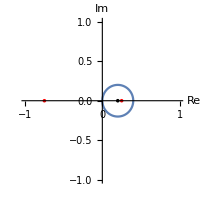

```mathematica
Show[p4,p1p]
```

```mathematica
Residue[Tan[2 π z],{z,1/4}]
```

-1/(2 π)

According to numbered line (6) on p. 723,

∮_C f[z]ⅆz=2 π ⅈ ∑_(j=1)^k Residue_(z=z_j)[f[z]] where j to k covers the number of relevant singularities

So in this case it is just a matter of

```mathematica
2π ⅈ(-1/(2 π))
```

-ⅈ

17.  ∮_C ⅇ^z/Cos[z]ⅆz , C: |z-(π ⅈ)/2|=4.5

```mathematica
Clear["Global`*"]
```

First I will investigate the singularities.

```mathematica
Solve[Cos[z]==0,z]
```

{{z→ConditionalExpression[-π/2+2 π C[1],C[1]∈Integers]},{z→ConditionalExpression[π/2+2 π C[1],C[1]∈Integers]}}

I can put together a plot of the path of the integral.

```mathematica
p5=ParametricPlot[{4.5 Cos[t],4.5 Sin[t]+π/2},{t,-π,π},ImageSize->200,Epilog->{PointSize[0.013],Point[{{0,π/2}}]},AxesLabel->{"Re","Im"},PlotRange->{-10,10},PlotStyle->{Thickness[0.004]}];
```

And generate a plot of the singularities.

```mathematica
p1p=ListPlot[Table[{Re[π/2+2 n π],Im[π/2+2 n π]},{n,-10,10}],PlotStyle->{Red}];
```

This time, since the plotted points differ, it is necessary to look at both plots.

```mathematica
p2p=ListPlot[Table[{Re[-π/2+2 n π],Im[-π/2+2 n π]},{n,-10,10}],PlotStyle->{Blue}];
```

And show both plots together.

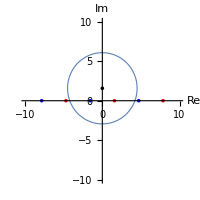

```mathematica
Show[p5, p1p,p2p]
```

The relevant singularities occur when n = 0, thus at -π/2+0ⅈ and π/2+0ⅈ

```mathematica
Residue[ⅇ^z/Cos[z],{z,-π/2}]
```

ⅇ^(-π/2)

```mathematica
Residue[ⅇ^z/Cos[z],{z,π/2}]
```

-ⅇ^(π/2)

So this time the assemblage will be equal to

```mathematica
2 π ⅈ(ⅇ^(-π/2)+-ⅇ^(π/2))
```

2 ⅈ (ⅇ^(-π/2)-ⅇ^(π/2)) π

```mathematica
FullSimplify[%]
```

-4 ⅈ π Sinh[π/2]

19.  ∮_C Sinh[z]/(2 z-ⅈ)ⅆz  , C: |z-2 ⅈ|=2

```mathematica
Clear["Global`*"]
```

First I will investigate the singularities.

```mathematica
Solve[2 z-ⅈ==0,z]
```

{{z→ⅈ/2}}

I can put together a plot of the path of the integral.

```mathematica
p7=ParametricPlot[{2 Cos[t],2 Sin[t]+2},{t,-2π,2π},ImageSize->200,Epilog->{PointSize[0.013],Point[{{0,2}}]},AxesLabel->{"Re","Im"},PlotRange->{-2π,2π},PlotStyle->{Thickness[0.004]}];
```

And generate a plot of the singularities.

```mathematica
p1p=ListPlot[Table[{Re[ⅈ/2],Im[ⅈ/2]},{n,-10,10}],PlotStyle->{Red}];
```

And show both plots together.

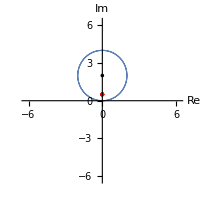

```mathematica
Show[p7, p1p]
```

The sole singularity is relevant.

```mathematica
Residue[Sinh[z]/(2 z-ⅈ),{z,ⅈ/2}]
```

1/2 ⅈ Sin[1/2]

Oddly, the residue calculated by Mathematica does not agree with the text answer. The text answer looks the same, except Sin[1/2]  is shown as Sinh[1/2]. Comparing the two for a possible typo,

```mathematica
N[Sin[1/2]]
```

0.479426

```mathematica
N[Sinh[1/2]]
```

0.521095

Hmm. Anyway, this time the developed answer will be equal to

```mathematica
2π ⅈ(1/2 ⅈ Sin[1/2])
```

-π Sin[1/2]

And in this answer, agreement is found with that of the text.

21.  ∮_C Cos[π z]/z^5 ⅆz  , C: |z|=1/2

```mathematica
Clear["Global`*"]
```

First I will investigate the singularities.

```mathematica
Solve[z^5==0,z]
```

{{z→0},{z→0},{z→0},{z→0},{z→0}}

I can put together a plot of the path of the integral.

```mathematica
p8=ParametricPlot[{1/2 Cos[t],1/2 Sin[t]},{t,-π,π},ImageSize->200,Epilog->{PointSize[0.013],Point[{{0,0}}]},AxesLabel->{"Re","Im"},PlotRange->{-1,1},PlotStyle->{Thickness[0.004]}];
```

And generate a plot of the singularities.

```mathematica
p1p=ListPlot[Table[{Re[0],Im[0]},{n,-2,2}],PlotStyle->{Red},PlotMarkers->{"×",12}];
```

And show both plots together.

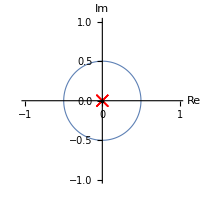

```mathematica
Show[p8, p1p]
```

The sole singularity is relevant.

```mathematica
Residue[Cos[π z]/z^5,{z,0}]
```

π^4/24

Another case where the residue as calculated by Mathematica does not match exactly with the text answer. In this case the text answer shows a z factor in the denominator. Ignoring this snag, the final assemblage will be equal to

```mathematica
2π ⅈ(π^4/24)
```

(ⅈ π^5)/12

The above answer matches that of the text.

23.  ∮_C (30 z^2-23 z+5)/((2 z-1)^2(3 z-1))ⅆz  , C: the unit circle

```mathematica
Clear["Global`*"]
```

First I will investigate the singularities.

```mathematica
Solve[(2 z-1)^2(3 z-1)==0,z]
```

{{z→1/3},{z→1/2},{z→1/2}}

I can put together a plot of the path of the integral.

```mathematica
p9=ParametricPlot[{1 Cos[t],1 Sin[t]},{t,-π,π},ImageSize->200,Epilog->{PointSize[0.013],Point[{{0,0}}]},AxesLabel->{"Re","Im"},PlotRange->{-1.5,1.5},PlotStyle->{Thickness[0.004]}];
```

And generate a plot of the singularities.

```mathematica
p1p=ListPlot[Table[{Re[1/3],Im[1/3]},{n,-10,10}],PlotStyle->{Red}];
```

```mathematica
p2p=ListPlot[Table[{Re[1/2],Im[1/2]},{n,-10,10}],PlotStyle->{Blue}];
```

And show three plots together.

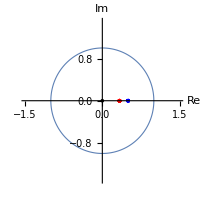

```mathematica
Show[p9,p1p,p2p]
```

Evidently two singularities are relevant.

```mathematica
Residue[(30 z^2-23 z+5)/((2 z-1)^2(3 z-1)),{z,1/3}]
```

2

```mathematica
Residue[(30 z^2-23 z+5)/((2 z-1)^2(3 z-1)),{z,1/2}]
```

1/2

The consolidated answer is

```mathematica
2π ⅈ(2+1/2)
```

5 ⅈ π

Green cells match text answers.

25.  ∮_C (z Cosh[π z])/(z^4+13 z^2+36)ⅆz  , C: |z|=π

```mathematica
Clear["Global`*"]
```

First I will investigate the singularities.

```mathematica
Solve[z^4+13 z^2+36==0,z]
```

{{z→-2 ⅈ},{z→2 ⅈ},{z→-3 ⅈ},{z→3 ⅈ}}

I can put together a plot of the path of the integral.

```mathematica
p10=ParametricPlot[{π Cos[t],π Sin[t]},{t,-π,π},ImageSize->200,Epilog->{PointSize[0.013],Point[{{0,0}}]},AxesLabel->{"Re","Im"},PlotRange->{-5,5},PlotStyle->{Thickness[0.004]}];
```

And generate plots of the singularities.

```mathematica
p1p=ListPlot[Table[{Re[-2 ⅈ],Im[-2 ⅈ]},{n,-10,10}],PlotStyle->{Red}];
```

```mathematica
p2p=ListPlot[Table[{Re[2 ⅈ],Im[2 ⅈ]},{n,-10,10}],PlotStyle->{Blue}];
```

```mathematica
p3p=ListPlot[Table[{Re[-3 ⅈ],Im[-3 ⅈ]},{n,-10,10}],PlotStyle->{Green}];
```

```mathematica
p4p=ListPlot[Table[{Re[3 ⅈ],Im[3 ⅈ]},{n,-10,10}],PlotStyle->{Purple}];
```

And show five plots together.

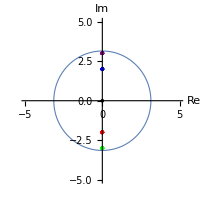

```mathematica
Show[p10,p1p,p2p,p3p,p4p]
```

The combined plot shows four relevant singularities.

```mathematica
Residue[(z Cosh[π z])/(z^4+13 z^2+36),{z,-2ⅈ}]
```

1/10

```mathematica
Residue[(z Cosh[π z])/(z^4+13 z^2+36),{z,2ⅈ}]
```

1/10

```mathematica
Residue[(z Cosh[π z])/(z^4+13 z^2+36),{z,-3ⅈ}]
```

1/10

```mathematica
Residue[(z Cosh[π z])/(z^4+13 z^2+36),{z,3ⅈ}]
```

1/10

So the consolidated answer will be

```mathematica
2π ⅈ(4/10)
```

(4 ⅈ π)/5